```mathematica
ClearAll["Global`*"]
```

### Load up packages

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
<<jvFuncs.wl
```

#### Helper func

```mathematica
makeErrorData[x_,y_,yErr_]:=Module[{zeList,xy,errorB},
xy=Partition[Riffle[x,y],2];
errorB=Map[ErrorBar,yErr];
zeList=Partition[Riffle[xy,errorB],2]
];
```

```mathematica
Needs["ComputerArithmetic`"]
```

```mathematica
orbit=3218;
```

## Initialize J-V, J_E-V data

### pot offset (in V)?

```mathematica
potTFactor=0;
```

### And the data ...

```mathematica
time={"00:11:50.194","00:11:50.825","00:11:51.456","00:11:52.087","00:11:52.717","00:11:53.348","00:11:53.979","00:11:54.610","00:11:55.240","00:11:55.871","00:11:56.502","00:11:57.133","00:11:57.763","00:11:58.394","00:11:59.025","00:11:59.656","00:12:00.287","00:12:00.917","00:12:01.548","00:12:02.179","00:12:02.810","00:12:03.440","00:12:04.071","00:12:04.702","00:12:05.333","00:12:05.963","00:12:06.594","00:12:07.225","00:12:07.856","00:12:08.486","00:12:09.117","00:12:09.748","00:12:10.379","00:12:11.009","00:12:11.640","00:12:12.271","00:12:12.902","00:12:13.532","00:12:14.163","00:12:14.794","00:12:15.425","00:12:16.056","00:12:16.686","00:12:17.317","00:12:17.948","00:12:18.579","00:12:19.209","00:12:19.840","00:12:20.471","00:12:21.102","00:12:21.732","00:12:22.363","00:12:22.994","00:12:23.625","00:12:24.255","00:12:24.886","00:12:25.517","00:12:26.148","00:12:26.778","00:12:27.409","00:12:28.040","00:12:28.671","00:12:29.301","00:12:29.932","00:12:30.563","00:12:31.194","00:12:31.825","00:12:32.455","00:12:33.086","00:12:33.717","00:12:34.348","00:12:34.978","00:12:35.609","00:12:36.240","00:12:36.871","00:12:37.501","00:12:38.132","00:12:38.763","00:12:39.078","00:12:39.709","00:12:40.340","00:12:40.971","00:12:41.601","00:12:42.232","00:12:42.863","00:12:43.494","00:12:44.124","00:12:44.755","00:12:45.386","00:12:46.017","00:12:46.647","00:12:47.278","00:12:47.909","00:12:48.540","00:12:49.170","00:12:49.801","00:12:50.432","00:12:51.063","00:12:51.693","00:12:52.324","00:12:52.955","00:12:53.586","00:12:54.217","00:12:54.847","00:12:55.478","00:12:56.109","00:12:56.740","00:12:57.370","00:12:58.001","00:12:58.632","00:12:59.263","00:12:59.893","00:13:00.524","00:13:01.155","00:13:01.786","00:13:02.416","00:13:03.047","00:13:03.678","00:13:04.309","00:13:04.939","00:13:05.570","00:13:06.201","00:13:06.832","00:13:07.462","00:13:08.093","00:13:08.724","00:13:09.355","00:13:09.985","00:13:10.616","00:13:11.247","00:13:11.878","00:13:12.509","00:13:13.139","00:13:13.770","00:13:14.401","00:13:15.032","00:13:15.662","00:13:16.293","00:13:16.924","00:13:17.555","00:13:18.185","00:13:18.816","00:13:19.447","00:13:20.078","00:13:20.708","00:13:21.339","00:13:21.970","00:13:22.601","00:13:23.231","00:13:23.862","00:13:24.493","00:13:25.124","00:13:25.754","00:13:26.385","00:13:27.016","00:13:27.647","00:13:28.277","00:13:28.908","00:13:29.539","00:13:30.170","00:13:30.800","00:13:31.431","00:13:32.062","00:13:32.693","00:13:33.323","00:13:33.954","00:13:34.585","00:13:35.216","00:13:35.846","00:13:36.477","00:13:37.108","00:13:37.739","00:13:38.370","00:13:39.000","00:13:39.631","00:13:40.262","00:13:40.893","00:13:41.523"};
pots={70.56,117.60,172.48,235.20,203.84,282.24,282.24,344.96,344.96,344.96,344.96,282.24,344.96,282.24,235.20,282.24,344.96,407.68,344.96,344.96,344.96,344.96,344.96,407.68,407.68,344.96,344.96,344.96,344.96,344.96,344.96,282.24,282.24,235.20,203.84,203.84,172.48,141.12,101.92,172.48,203.84,203.84,86.24,101.92,101.92,86.24,86.24,101.92,172.48,172.48,203.84,203.84,235.20,235.20,282.24,282.24,282.24,282.24,344.96,407.68,407.68,344.96,344.96,344.96,407.68,407.68,407.68,407.68,407.68,470.40,470.40,470.40,407.68,407.68,407.68,407.68,407.68,407.68,407.68,407.68,407.68,407.68,407.68,407.68,407.68,470.40,407.68,407.68,407.68,407.68,407.68,407.68,407.68,407.68,407.68,407.68,344.96,344.96,344.96,344.96,344.96,344.96,344.96,344.96,344.96,344.96,344.96,407.68,407.68,407.68,407.68,407.68,407.68,344.96,344.96,282.24,344.96,344.96,172.48,172.48,101.92,101.92,70.56,101.92,235.20,344.96,344.96,344.96,407.68,407.68,407.68,344.96,344.96,344.96,282.24,282.24,282.24,235.20,235.20,235.20,235.20,235.20,235.20,235.20,235.20,282.24,235.20,235.20,235.20,282.24,235.20,203.84,141.12,70.56,70.56,70.56,86.24,70.56,70.56,86.24,86.24,86.24,101.92,70.56,70.56,70.56,86.24,86.24,101.92,117.60,101.92,117.60,141.12,117.60,101.92,70.56,70.56,70.56};
curs={0.151,1.264,2.651,1.495,0.762,1.326,1.550,1.722,1.780,2.292,2.104,2.169,2.080,3.277,3.322,3.121,2.312,2.661,1.991,1.951,2.307,2.376,2.347,2.987,3.152,2.341,2.530,2.285,2.211,2.508,2.234,1.996,1.359,0.979,0.850,0.795,0.623,0.462,0.311,0.586,0.817,1.082,0.720,0.652,0.416,0.373,0.441,0.438,0.553,0.732,0.779,0.915,1.110,1.063,1.370,1.531,1.226,1.151,1.685,2.729,2.737,2.226,2.103,2.541,2.358,2.254,2.003,2.133,2.146,2.239,2.561,2.627,2.465,2.354,1.985,1.945,1.912,1.420,2.016,2.158,2.361,2.341,2.300,2.239,2.252,2.285,2.306,2.238,2.304,2.176,2.128,1.976,2.018,2.153,2.246,2.000,1.707,1.541,1.429,1.378,1.400,1.334,1.314,1.463,1.543,1.880,1.799,1.887,2.241,2.400,2.643,2.685,2.582,2.646,2.418,2.243,2.380,1.972,1.044,1.336,0.681,1.021,0.932,1.315,2.864,2.927,3.759,3.385,3.317,3.436,2.896,2.532,2.213,2.142,1.929,1.719,1.609,1.423,1.279,1.273,1.323,1.247,1.343,1.589,1.730,1.993,1.678,1.877,1.793,2.066,1.967,1.506,1.040,0.247,0.270,0.244,0.372,0.154,0.157,0.133,0.083,0.088,0.075,0.074,0.152,0.258,0.345,0.331,0.351,0.508,0.624,0.689,0.939,0.915,0.946,1.139,0.454,0.159};
curErrs={0.038,0.057,0.109,0.078,0.049,0.053,0.059,0.063,0.099,0.155,0.112,0.112,0.100,0.083,0.105,0.108,0.130,0.154,0.129,0.100,0.114,0.100,0.099,0.108,0.224,0.131,0.160,0.148,0.128,0.097,0.099,0.093,0.108,0.086,0.087,0.056,0.059,0.031,0.025,0.051,0.143,0.140,0.097,0.158,0.049,0.036,0.114,0.062,0.192,0.123,0.145,0.161,0.165,0.113,0.116,0.120,0.062,0.057,0.071,0.083,0.080,0.059,0.062,0.077,0.104,0.085,0.081,0.077,0.080,0.072,0.074,0.076,0.102,0.092,0.080,0.075,0.077,0.075,0.085,0.068,0.084,0.129,0.120,0.103,0.091,0.094,0.084,0.077,0.087,0.103,0.090,0.081,0.074,0.085,0.077,0.069,0.060,0.173,0.118,0.111,0.098,0.098,0.073,0.073,0.083,0.065,0.059,0.052,0.059,0.058,0.064,0.060,0.061,0.076,0.072,0.078,0.073,0.056,0.034,0.058,0.059,0.026,0.049,0.100,0.106,0.049,0.075,0.115,0.089,0.090,0.096,0.098,0.077,0.064,0.066,0.063,0.063,0.088,0.065,0.062,0.059,0.049,0.060,0.057,0.075,0.088,0.094,0.099,0.078,0.072,0.077,0.064,0.069,0.029,0.181,0.046,0.037,0.019,0.035,0.036,0.026,0.015,0.053,0.023,0.027,0.043,0.030,0.035,0.029,0.074,0.181,0.072,0.081,0.047,0.058,0.997,0.054,0.039};
jes={0.036,0.167,0.432,0.329,0.156,0.322,0.420,0.494,0.534,0.708,0.573,0.543,0.551,0.820,0.769,0.786,0.668,0.822,0.583,0.558,0.678,0.719,0.682,0.905,0.903,0.653,0.754,0.635,0.639,0.751,0.632,0.524,0.324,0.225,0.181,0.156,0.119,0.083,0.055,0.104,0.161,0.196,0.093,0.090,0.067,0.059,0.069,0.070,0.104,0.134,0.160,0.197,0.260,0.257,0.353,0.405,0.308,0.294,0.504,0.962,0.908,0.652,0.589,0.729,0.745,0.762,0.656,0.716,0.765,0.822,0.960,0.983,0.891,0.846,0.684,0.686,0.695,0.492,0.737,0.768,0.813,0.809,0.802,0.780,0.811,0.852,0.841,0.794,0.809,0.756,0.724,0.661,0.700,0.754,0.796,0.661,0.555,0.484,0.458,0.414,0.435,0.414,0.399,0.441,0.476,0.610,0.591,0.621,0.787,0.857,0.914,0.896,0.804,0.754,0.571,0.536,0.643,0.514,0.185,0.235,0.104,0.146,0.128,0.199,0.606,0.713,0.841,0.887,1.030,0.966,0.820,0.661,0.589,0.564,0.489,0.412,0.386,0.322,0.276,0.277,0.297,0.266,0.276,0.339,0.377,0.444,0.354,0.373,0.373,0.453,0.400,0.269,0.172,0.042,0.051,0.050,0.061,0.033,0.034,0.028,0.022,0.023,0.028,0.020,0.033,0.044,0.057,0.056,0.060,0.079,0.099,0.104,0.150,0.136,0.132,0.121,0.061,0.034};
jeErrs={0.036,0.042,0.532,0.079,0.043,0.069,0.085,0.088,0.131,0.288,0.206,0.131,0.093,0.081,0.121,0.120,0.199,3.070,0.275,0.113,0.112,0.151,0.231,0.121,0.318,0.602,0.835,0.158,0.129,0.145,0.430,0.111,0.152,0.126,0.100,0.050,0.045,0.042,0.020,0.041,0.147,2.308,0.074,0.141,4.261,0.181,0.064,0.044,0.123,0.115,0.170,0.189,0.179,0.151,0.158,0.154,0.077,0.072,0.094,0.095,0.088,0.069,0.079,0.089,0.115,0.132,0.106,0.086,0.089,0.098,0.111,0.094,0.135,0.141,0.124,0.086,0.082,0.082,0.164,0.098,0.096,0.201,0.457,0.138,0.094,0.105,0.145,0.116,0.112,0.128,0.195,0.117,0.081,0.097,0.126,0.091,0.070,1.919,0.190,0.268,0.105,0.111,0.312,0.132,0.087,0.091,0.105,0.075,0.073,0.080,0.110,0.087,0.071,0.094,0.099,0.082,0.069,0.059,0.035,0.051,0.036,0.039,0.073,0.165,0.090,0.054,0.080,0.125,0.099,0.107,0.142,0.106,0.070,0.069,0.125,0.079,0.065,0.106,0.112,0.578,0.057,0.052,0.084,0.062,0.064,0.110,0.141,0.121,0.062,0.074,0.081,0.061,0.049,0.025,0.093,0.053,0.032,0.022,0.025,0.105,0.022,0.022,1.122,0.017,0.029,0.037,0.039,0.023,0.064,0.051,0.063,0.072,0.092,0.060,0.057,2.049,0.050,0.053};
gaussbulkEs={101.92,93.67,134.25,185.94,172.37,214.18,268.14,289.03,271.39,336.16,281.06,322.52,258.16,293.86,221.37,282.01,338.50,395.20,303.51,272.12,371.16,319.00,348.23,379.38,101.92,335.74,307.30,333.50,321.92,351.46,314.67,259.30,248.08,240.33,148.86,188.22,175.04,142.91,111.43,101.92,126.62,50.96,101.68,111.80,117.60,91.44,112.27,121.19,171.76,167.32,236.51,173.72,217.66,234.28,331.86,307.23,253.84,335.08,310.96,373.92,330.21,393.30,284.95,379.22,350.87,392.02,414.86,352.75,394.72,530.17,471.43,425.16,378.56,391.67,412.46,377.52,386.38,415.53,360.48,382.16,419.85,404.64,412.16,346.50,437.29,422.20,411.39,415.98,440.85,384.66,412.50,379.99,341.28,412.40,388.26,343.54,353.65,393.76,398.39,360.18,290.04,333.20,282.56,420.63,367.63,301.82,300.04,311.30,358.40,385.54,366.01,422.91,377.72,318.89,172.48,164.14,289.48,374.58,181.20,167.73,71.12,98.17,100.87,101.92,76.35,235.05,172.48,85.17,387.37,84.79,68.01,325.88,263.87,95.96,315.94,328.07,252.88,235.26,225.17,239.51,217.39,163.93,84.54,236.31,243.61,82.21,239.21,109.47,101.92,101.92,101.92,97.39,89.10,55.28,51.00,52.74,101.04,75.04,51.03,50.96,101.92,64.11,101.92,101.92,50.96,101.92,101.92,88.10,115.98,114.27,97.21,108.90,165.45,107.45,98.45,77.24,86.63,54.82};
kappabulkEs={79.42,68.33,128.96,168.42,142.83,225.36,283.79,276.31,337.42,342.35,284.38,283.39,272.56,268.65,210.19,271.89,351.71,384.63,337.63,339.00,331.72,330.76,322.49,372.04,94.66,336.73,336.20,336.11,341.37,322.48,339.80,276.27,226.57,237.35,195.06,197.24,154.52,119.74,82.93,73.84,177.18,85.03,58.86,90.31,59.03,50.96,59.12,71.20,129.98,159.00,181.53,196.75,226.03,229.27,277.25,290.54,295.85,275.81,316.06,368.13,297.99,343.67,272.59,317.54,319.12,373.57,371.84,364.16,371.88,463.56,468.39,477.89,371.75,365.06,380.17,362.48,369.51,360.47,369.27,376.03,379.98,369.56,389.30,353.51,364.54,356.83,371.63,384.58,373.54,379.19,380.16,368.53,387.38,380.11,367.43,384.30,331.05,325.87,325.63,329.19,334.79,339.69,336.59,327.75,312.26,335.00,328.39,324.79,366.91,374.28,368.23,373.53,376.72,329.27,125.59,96.55,332.95,335.32,146.31,167.31,51.20,66.80,50.96,61.80,54.37,142.75,114.31,73.40,371.31,50.96,58.12,340.71,326.70,77.46,291.72,288.50,268.62,228.98,212.56,180.30,240.61,173.17,91.17,223.84,209.75,50.96,214.91,58.80,61.53,65.11,80.80,101.91,77.90,50.96,50.96,51.00,67.32,66.93,50.96,73.38,50.96,66.09,58.53,50.96,67.37,67.90,51.88,51.23,91.54,85.81,73.13,89.43,147.26,98.11,70.56,70.94,73.83,60.08};
```

## Manip plots to decide on indices to use

### Check out J-V relation

```mathematica
ind1Start=0;ind1End=150;ind1Init=72;ind2Init=198;(*Jim alt?*)
```

```mathematica
Manipulate[ErrorListPlot[(makeErrorData[pots[[#1;;#2]],curs[[#1;;#2]],curErrs[[#1;;#2]]])&[ind1,ind2],AxesStyle->(FontSize->24),PlotRange->{{000,Max[pots]*1.1},{0,Max[curs]*1.1}},Epilog->Style[Text[StringJoin@Riffle[time[[{ind1,ind2}]],"–"],Scaled[{0.05,0.95}],{-1,1}],24],ImageSize->700],{{ind1,ind1Init},ind1Start,ind1End,1},{{ind2,ind2Init},ind1End+1,Length@pots,1}]
```

### Check out energy flux–voltage relation

```mathematica
Manipulate[ErrorListPlot[(makeErrorData[pots[[#1;;#2]],jes[[#1;;#2]],jeErrs[[#1;;#2]]])&[ind1,ind2],PlotRange->{{0,Max[pots]},{0,Max[jes]}},Epilog->Style[Text[StringJoin@Riffle[time[[{ind1,ind2}]],"–"],Scaled[{0.05,0.95}],{-1,1}],24],ImageSize->700],{{ind1,ind1Init},ind1Start,ind1End,1},{{ind2,ind2Init},ind1End+1,Length@pots,1}]
```

The fits—J-V, J_E-V, and combined

## Initialize data for portions of arc in which we are interested

### Setup indices

```mathematica
inds1=Range[100,132];
```

```mathematica
inds2=Range[137,150];
```

```mathematica
inds2=Range[162,198]; (*Alt*)
```

```mathematica
inds3={3,4}~Join~inds2;
```

### Initialize plotData1, errorData1, plotDataWts1, etc.

Current data

```mathematica
{plotData1,plotData2,plotData3}=(Partition[Riffle[pots[[#]],curs[[#]]],2])&/@{inds1,inds2,inds3};
```

```mathematica
{errorData1,errorData2,errorData3}=(makeErrorData[pots[[#]],curs[[#]],curErrs[[#]]])&/@{inds1,inds2,inds3};
```

```mathematica
{plotDataWts1,plotDataWts2,plotDataWts3}=(1/(curErrs[[#]])^2)&/@{inds1,inds2,inds3};
```

Energy flux data

```mathematica
{jeData1,jeData2,jeData3}=(Partition[Riffle[pots[[#]],jes[[#]]],2])&/@{inds1,inds2,inds3};
```

```mathematica
{errorJe1,errorJe2,errorJe3}=(makeErrorData[pots[[#]],jes[[#]],jeErrs[[#]]])&/@{inds1,inds2,inds3};
```

```mathematica
{jeDataWts1,jeDataWts2,jeDataWts3}=(1/(jeErrs[[#]])^2)&/@{inds1,inds2,inds3};
```

## Fits: Select indices to use, setup bounds and initial guesses

### Which to use?

```mathematica
useinds1=0; (*Else use inds2*)
```

### Bounds

```mathematica
minFitT=100;
maxFitT=5000;
minFitRB=3;
maxFitRB=1000000;
minFitN=0.01;
maxFitN=10;
minFitKappa=1.501;
maxFitKappa=35;
```

```mathematica
kConstraints={minFitRB<kFitRB<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gConstraints={minFitRB<gFitRB<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

```mathematica
kCombConstraints={minFitRB<kFitRB<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gCombConstraints={minFitRB<gFitRB<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

```mathematica
kDoubledConstraints={minFitRB<kFitRB1<maxFitRB,minFitRB<kFitRB2<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gDoubledConstraints={minFitRB<gFitRB1<maxFitRB,minFitRB<gFitRB2<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

### Initial guesses

```mathematica
kFitNinit=1;
kFitTinit=300;
kFitRBinit=10;
kFitKappainit=10;
kFitRB1init=10;
kFitRB2init=10;
```

```mathematica
gFitNinit=1;
gFitTinit=300;
gFitRBinit=10;
gFitRB1init=10;
gFitRB2init=10;
```

#### Init fit data

Maxwellian-ish thing?

```mathematica
If[useinds1==1,Print["Using inds1 ..."];indsInUse=inds1;jData=plotData1;jWts=plotDataWts1;jErrData=errorData1;jeData=jeData1;jeWts=jeDataWts1;jeErrData=errorJe1;,Print["Using inds2 ..."];indsInUse=inds2;jData=plotData2;jWts=plotDataWts2;jErrData=errorData2;jeData=jeData2;jeWts=jeDataWts2;jeErrData=errorJe2;];
```

Using inds2 ...

## Nonlinear J-V fits

### Now the actual fits

```mathematica
(*kConstraints={0.01<kFitN<10,10<kFitT<4000,3<kFitRB<1000000,1.501<kFitKappa<20};
gConstraints={0.01<gFitN<10,10<gFitT<4000,3<gFitRB<1000000};*)
```

```mathematica
kModel = JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
```

```mathematica
gModel = JVMaxwellian[pot,gFitRB,gFitT,gFitN];
```

```mathematica
kFit=NonlinearModelFit[jData,{kModel,kConstraints},{{kFitN,kFitNinit},{kFitT,kFitTinit},{kFitRB,kFitRBinit},{kFitKappa,kFitKappainit}},pot,Weights->jWts];
```

```mathematica
gFit=NonlinearModelFit[jData,{gModel,gConstraints},{{gFitN,gFitNinit},{gFitT,gFitTinit},{gFitRB,gFitRBinit}},pot,Weights->jWts];
```

```mathematica
kDOF=Length[pots[[inds1]]]-4;
```

```mathematica
gDOF=Length[pots[[inds1]]]-3;
```

```mathematica
{kBestN,kBestT,kBestRB,kBestKappa,kBestChi2red}=Values@kFit["BestFitParameters"]~Join~{Total[(kFit["FitResiduals"])^2*jWts]/kDOF};
```

```mathematica
{gBestN,gBestT,gBestRB,gBestChi2red}=Values@gFit["BestFitParameters"]~Join~{Total[(gFit["FitResiduals"])^2*jWts]/gDOF};
```

## Nonlinear J_E-V fits

### Initial guesses

```mathematica
(*kFitNinit=1;
kFitTinit=300;
kFitRBinit=10;
kFitKappainit=10;*)
```

```mathematica
(*gFitNinit=1;
gFitTinit=300;
gFitRBinit=10;*)
```

### Now the actual fits

```mathematica
(*kConstraints={0.01<kFitN<10,100<kFitT<4000,3<kFitRB<1000,1.51<kFitKappa<20};
gConstraints={0.01<gFitN<10,100<gFitT<4000,3<gFitRB<1000};*)
```

```mathematica
kModelJeV = JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
```

```mathematica
gModelJeV = JEVMaxwellian[pot,gFitRB,gFitT,gFitN];
```

```mathematica
kFitJeV=NonlinearModelFit[jeData,{kModelJeV,kConstraints},{{kFitN,kFitNinit},{kFitT,kFitTinit},{kFitRB,kFitRBinit},{kFitKappa,kFitKappainit}},pot,Weights->jeWts];
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

```mathematica
gFitJeV=NonlinearModelFit[jeData,{gModelJeV,gConstraints},{{gFitN,gFitNinit},{gFitT,gFitRBinit},{gFitRB,gFitRBinit}},pot,Weights->jeWts];
```

```mathematica
kDOF=Length[pots[[inds1]]]-4;
```

```mathematica
gDOF=Length[pots[[inds1]]]-3;
```

```mathematica
{kBestJeVN,kBestJeVT,kBestJeVRB,kBestJeVKappa,kBestJeVChi2red}=Values@kFitJeV["BestFitParameters"]~Join~{Total[(kFitJeV["FitResiduals"])^2*jeWts]/kDOF};
```

```mathematica
{gBestJeVN,gBestJeVT,gBestJeVRB,gBestJeVChi2red}=Values@gFitJeV["BestFitParameters"]~Join~{Total[(gFitJeV["FitResiduals"])^2*jeWts]/gDOF};
```

## Now J-V and J_E-V fits simultaneously!

```mathematica
(*RBinit=kBestRB;Tminit=kBestT;nminit=kBestN;kappainit=kBestKappa;*)
```

```mathematica
(*RBinit=kBestJeVRB;Tminit=kBestJeVT;nminit=kBestJeVN;kappainit=kBestJeVKappa;*)
```

```mathematica
combDat = Join[jData/.{x_,y_}->{1,x,y},jeData/.{x_,y_}->{2,x,y}];
```

```mathematica
combWts=jWts~Join~jeWts;
```

```mathematica
kCombFitModel[set_,pot_,kFitRB,kFitT_,kFitN_,kFitKappa_]:=Which[set==1,Evaluate@JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa],set==2,Evaluate@JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa]];
```

```mathematica
gCombFitModel[set_,pot_,gFitRB,gFitT_,gFitN_]:=Which[set==1,Evaluate@JVMaxwellian[pot,gFitRB,gFitT,gFitN],set==2,Evaluate@JEVMaxwellian[pot,gFitRB,gFitT,gFitN]];
```

```mathematica
kCombFit=NonlinearModelFit[combDat,{kCombFitModel[set,pot,kFitRB,kFitT,kFitN,kFitKappa],kCombConstraints},{{kFitRB,kFitRBinit},{kFitT,kFitTinit},{kFitN,kFitNinit},{kFitKappa,kFitKappainit}},{set,pot},Weights->combWts];
```

```mathematica
gCombFit=NonlinearModelFit[combDat,{gCombFitModel[set,pot,gFitRB,gFitT,gFitN],gCombConstraints},{{gFitRB,gFitRBinit},{gFitT,gFitTinit},{gFitN,gFitNinit}},{set,pot},Weights->combWts];
```

```mathematica
kCombDOF=Length[combDat[[;;,1]]]-4;
```

```mathematica
gCombDOF=Length[combDat[[;;,1]]]-3;
```

```mathematica
{kCombRB,kCombT,kCombN,kCombKappa,kCombChi2red}=Values@kCombFit["BestFitParameters"]~Join~{Total[(kCombFit["FitResiduals"])^2*combWts]/kCombDOF};
```

```mathematica
{gCombRB,gCombT,gCombN,gCombChi2red}=Values@gCombFit["BestFitParameters"]~Join~{Total[(gCombFit["FitResiduals"])^2*combWts]/gCombDOF};
```

Plots

### Setup plot ranges

```mathematica
minPot=Min[pots[[;;]] ]* 8/10;maxPot=6000;
```

```mathematica
minJ=0;maxJ=6;
```

```mathematica
minJe=0;maxJe=19.;
```

### Setup combined fit plots

```mathematica
parNames={"T_m : ","n_m : ","R_B : ","χ_red^2:"};
vSpace=0.5;
pTableFontSize=16;
```

```mathematica
JVRepl={gRB->gBestRB,gTm->gBestT,gnm->gBestN,gChi2->gBestChi2red,kRB->kBestRB,kTm->kBestT,knm->kBestN,kappa->kBestKappa,kChi2->kBestChi2red};
```

```mathematica
JeVRepl={gRB->gBestJeVRB,gTm->gBestJeVT,gnm->gBestJeVN,gChi2->gBestJeVChi2red,kRB->kBestJeVRB,kTm->kBestJeVT,knm->kBestJeVN,kappa->kBestJeVKappa,kChi2->kBestJeVChi2red};
```

```mathematica
combRepl={gRB->gCombRB,gTm->gCombT,gnm->gCombN,gChi2->gCombChi2red,kRB->kCombRB,kTm->kCombT,knm->kCombN,kappa->kCombKappa,kChi2->kCombChi2red};
```

```mathematica
(*gVals=MapThread[NumberForm,{({gTm,gnm,gRB}/.combRepl),{{3,0},{3,2},{3,1}}}];
kVals=MapThread[NumberForm,{({kTm,knm,kRB}/.combRepl),{{3,0},{3,2},{3,1}}}];*)
```

```mathematica
gJVVals=(MapThread[NumberForm,{({gTm,gnm}/.JVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[gRB,3]/.JVRepl}~Join~{NumberForm[gChi2,3]/.JVRepl};
kJVVals=(MapThread[NumberForm,{({kTm,knm}/.JVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[kRB,3]/.JVRepl}~Join~{NumberForm[kChi2,3]/.JVRepl};
```

```mathematica
gJeVVals=(MapThread[NumberForm,{({gTm,gnm}/.JeVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[gRB,3]/.JeVRepl}~Join~{NumberForm[gChi2,3]/.JeVRepl};
kJeVVals=(MapThread[NumberForm,{({kTm,knm}/.JeVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[kRB,3]/.JeVRepl}~Join~{NumberForm[kChi2,4]/.JeVRepl};
```

```mathematica
gCombVals=(MapThread[NumberForm,{({gTm,gnm}/.combRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[gRB,3]/.combRepl}~Join~{NumberForm[gChi2,4]/.combRepl};
kCombVals=(MapThread[NumberForm,{({kTm,knm}/.combRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[kRB,3]/.combRepl}~Join~{NumberForm[kChi2,4]/.combRepl};
```

```mathematica
JVParTable=Text[Grid[Transpose[{{"Gauss"}~Join~parNames~Join~{"Kappa"}~Join~parNames,{""}~Join~gJVVals~Join~{""}~Join~kJVVals}],Alignment->".",Spacings->{0,vSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
JeVParTable=Text[Grid[Transpose[{{"Gauss"}~Join~parNames~Join~{"Kappa"}~Join~parNames,{""}~Join~gJeVVals~Join~{""}~Join~kJeVVals}],Alignment->".",Spacings->{0,vSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
combParTable=Text[Grid[Transpose[{{"Gauss"}~Join~parNames~Join~{"Kappa"}~Join~parNames,{""}~Join~gCombVals~Join~{""}~Join~kCombVals}],Alignment->".",Spacings->{0,vSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
combTitle=StringJoin@Riffle[time[[indsInUse[[{1,-1}]]]],"–"];
```

```mathematica
combFitJVPlot=Plot[Evaluate@(({JVMaxwellian[pot,gRB,gTm,gnm],JVKappa[pot,kRB,kTm,knm,kappa]})/.combRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJ,maxJ}},PlotLegends->Map[(Style[#,23])&,{"Maxwellian",StringForm["κ = `1`",NumberForm[(kappa/.combRepl),{3,3}]]}],Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"",Style[StringForm["J-V and J_E-V Simultaneous Fit (`1`)",combTitle],Bold,25]}},ImageSize->800,FrameStyle->Directive[Black,23],FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},Epilog->Inset[combParTable,Scaled[{0.12,0.7}]]];
```

```mathematica
combFitJeVPlot=Plot[Evaluate@(({JEVMaxwellian[pot,gRB,gTm,gnm],JEVKappa[pot,kRB,kTm,knm,kappa]})/.combRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJe,maxJe}},Frame->True,FrameLabel->{{"j_(E||, i) (mW/m^2)",""},{"ΔΦ (V)",""}},ImageSize->800,FrameStyle->Directive[Black,23]];
```

```mathematica
combJVPlot=Show[combFitJVPlot,ErrorListPlot[jErrData,PlotStyle->Gray]];
```

```mathematica
combJeVPlot=Show[combFitJeVPlot,ErrorListPlot[jeErrData,PlotStyle->Gray]];
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/plots/"<>(ToString@DateString[{"Year","Month","Day","/"}]);
```

```mathematica
If[!FileExistsQ[dir],Print["Nei!"];CreateDirectory[dir];Print["Nå har du det!"],Print["Ja!"]]
```

Ja!

```mathematica
orbPref=ToString@StringForm["Orb`1`",orbit];
```

```mathematica
JVPref="JVFit";
JeVPref="JeVFit";
combPref="combJVJeVFit";
```

```mathematica
(*combJVPref="combJVJeVFit__JV";
combJeVPref="combJVJeVFit__JeV";*)
```

```mathematica
(*{JVFilename,JeVFilename,combJVFilename,combJeVFilename}=(ToString@StringForm["`1`__`2`__inds_`3`-`4`.png",orbPref,#,indsInUse[[1]],indsInUse[[-1]]])&/@{JVPref,JeVPref,combJVPref,combJeVPref}*)
```

```mathematica
If[potTFactor == 0,suffString="",suffString=ToString@StringForm["__`1`V_offset",potTFactor]];
```

```mathematica
{JVFilename,JeVFilename,combFilename}=(ToString@StringForm["`1`__`2``3`__inds_`4`-`5`.png",orbPref,#,suffString,indsInUse[[1]],indsInUse[[-1]]])&/@{JVPref,JeVPref,combPref}
```

{Orb11694__JVFit__inds_162-198.png,Orb11694__JeVFit__inds_162-198.png,Orb11694__combJVJeVFit__inds_162-198.png}

### J-V plot

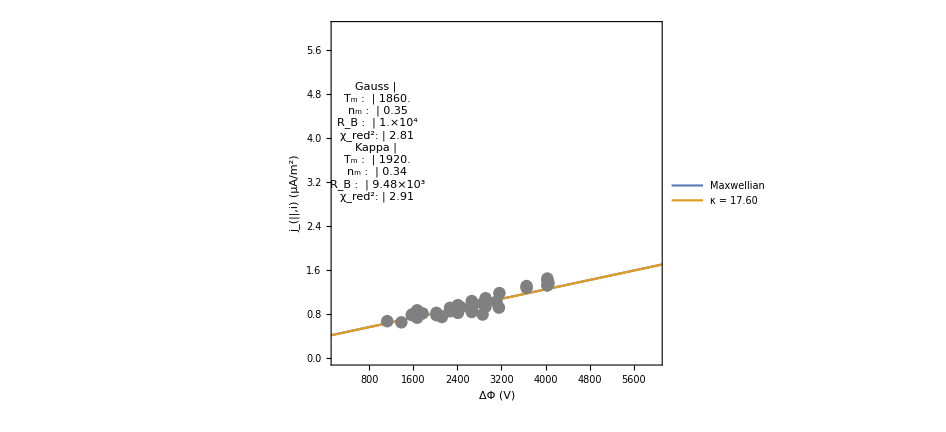

```mathematica
JVPlot=Show[Plot[{kFit[pot],gFit[pot]},{pot,20,10000},PlotRange->{{minPot,maxPot},{minJ,maxJ}},PlotLegends->((Style[#,20])&/@{"Maxwellian",StringForm["κ = `1`",NumberForm[kBestKappa,{3,2}]]}),Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["J-V Fit (`1`)",combTitle],Bold,25]}},ImageSize->700,FrameStyle->Directive[Black,23],Epilog->Inset[JVParTable,Scaled[{0.14,0.65}]]],ErrorListPlot[jErrData,PlotStyle->Gray]]
```

### J_E-V plot

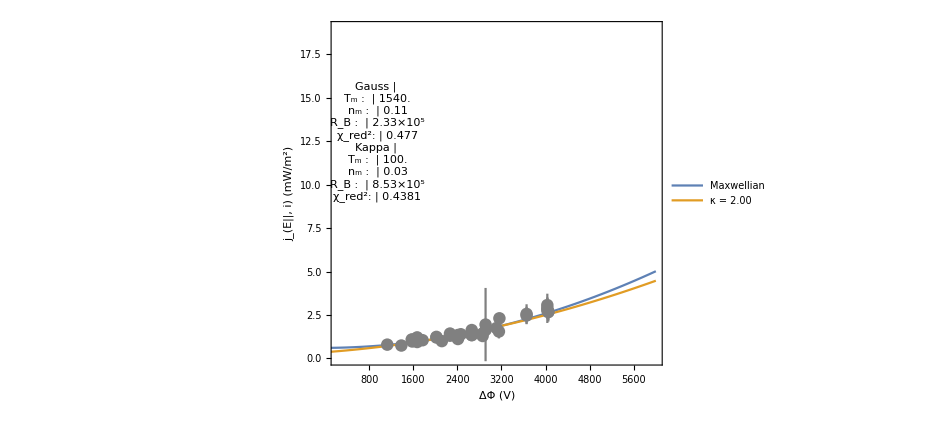

```mathematica
JeVPlot=Show[Plot[{kFitJeV[pot],gFitJeV[pot]},{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJe,maxJe}},PlotLegends->((Style[#,20])&/@{"Maxwellian",StringForm["κ = `1`",NumberForm[kBestJeVKappa,{3,2}]]}),Frame->True,FrameLabel->{{"j_(E||, i) (mW/m^2)",""},{"ΔΦ (V)",Style[StringForm["J_E-V Fit (`1`)",combTitle],Bold,25]}},ImageSize->700,FrameStyle->Directive[Black,23],Epilog->Inset[JeVParTable,Scaled[{0.14,0.65}]]],ErrorListPlot[jeErrData,PlotStyle->Gray]]
```

### Plots from combined fit

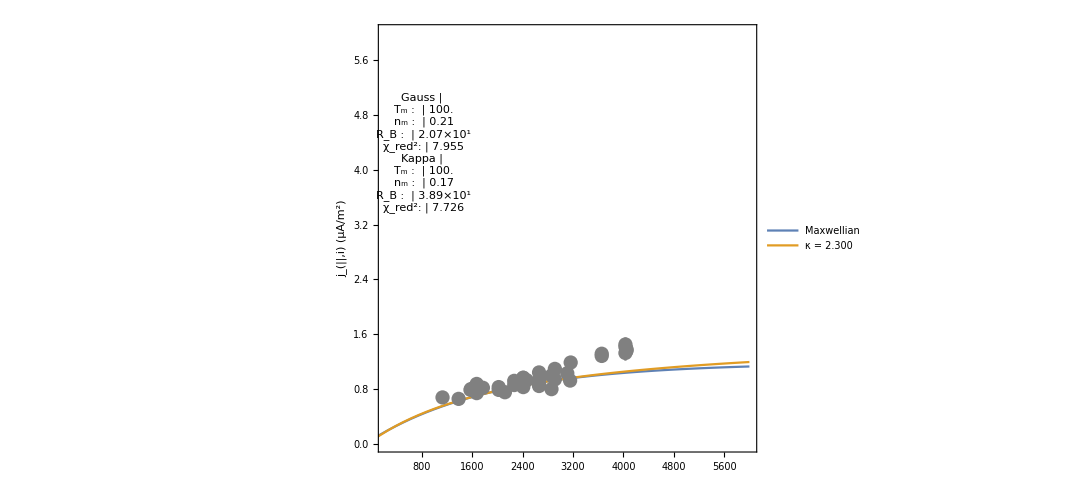
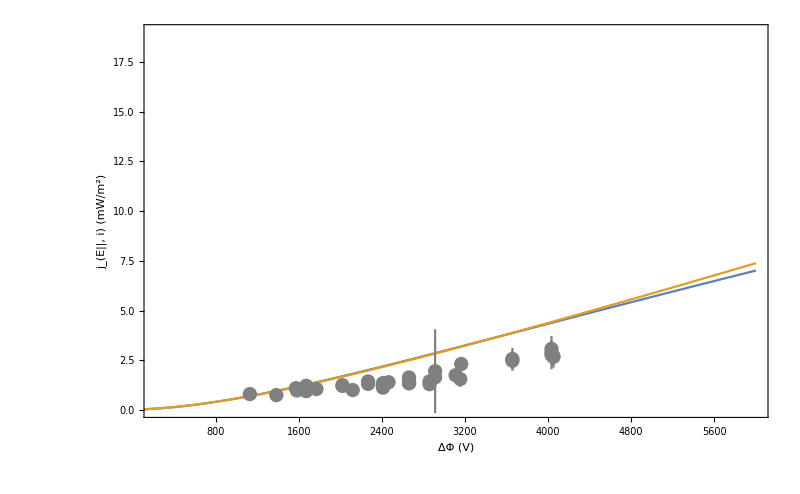

```mathematica
combPlot=Column[{combJVPlot,combJeVPlot}]
```

```mathematica
makePlots=1;
```

```mathematica
(*If[makePlots==1,Print["Making plots in "<>dir<>" ..."];Export[dir<>JVFilename,JVPlot];Export[dir<>JeVFilename,JeVPlot];Export[dir<>combJVFilename,combJVPlot];Export[dir<>combJeVFilename,combJeVPlot];Print["Done!"]]*)
```

```mathematica
If[makePlots==1,Print["Making plots in "<>dir<>" ..."];Export[dir<>JVFilename,JVPlot];Print[JeVFilename<>" ..."];Export[dir<>JeVFilename,JeVPlot];Print[combFilename<>" ..."];Export[dir<>combFilename,combPlot];
Print["Done!"]]
```

Making plots in /SPENCEdata/Research/Satellites/FAST/kappa_dists/plots/20180319/ ...

Orb11694__JeVFit__inds_162-198.png ...

Orb11694__combJVJeVFit__inds_162-198.png ...

Done!

Now everything at once

### Bounds

```mathematica
minFitT=5;
maxFitT=5000;
minFitRB=3;
maxFitRB=1000000;
minFitN=0.01;
maxFitN=10;
minFitKappa=1.501;
maxFitKappa=35;
```

```mathematica
kConstraints={minFitRB<kFitRB<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gConstraints={minFitRB<gFitRB<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

```mathematica
kCombConstraints={minFitRB<kFitRB<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gCombConstraints={minFitRB<gFitRB<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

```mathematica
kDoubledConstraints={minFitRB<kFitRB1<maxFitRB,minFitRB<kFitRB2<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gDoubledConstraints={minFitRB<gFitRB1<maxFitRB,minFitRB<gFitRB2<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

### Initial guesses

```mathematica
kFitNinit=1;
kFitTinit=300;
kFitRBinit=10;
kFitKappainit=10;
kFitRB1init=10;
kFitRB2init=10;
```

```mathematica
gFitNinit=1;
gFitTinit=300;
gFitRBinit=10;
gFitRB1init=10;
gFitRB2init=10;
```

### Setup indices

```mathematica
indsSeg1=Range[100,132];
```

```mathematica
indsSeg2=Range[137,150];
```

```mathematica
(*indsSeg2=Range[162,198]; (*Alt*)*)
```

### Initialize plotData1, errorData1, plotDataWts1, etc.

Current data

```mathematica
{jDataSeg1,jDataSeg2}=(Partition[Riffle[pots[[#]],curs[[#]]],2])&/@{indsSeg1,indsSeg2};
```

```mathematica
{jErrDataSeg1,jErrDataSeg2}=(makeErrorData[pots[[#]],curs[[#]],curErrs[[#]]])&/@{indsSeg1,indsSeg2};
```

```mathematica
{jWtsSeg1,jWtsSeg2}=(1/(curErrs[[#]])^2)&/@{indsSeg1,indsSeg2};
```

Energy flux data

```mathematica
{jeDataSeg1,jeDataSeg2}=(Partition[Riffle[pots[[#]],jes[[#]]],2])&/@{indsSeg1,indsSeg2};
```

```mathematica
{jeErrDataSeg1,jeErrDataSeg2}=(makeErrorData[pots[[#]],jes[[#]],jeErrs[[#]]])&/@{indsSeg1,indsSeg2};
```

```mathematica
{jeWtsSeg1,jeWtsSeg2}=(1/(jeErrs[[#]])^2)&/@{indsSeg1,indsSeg2};
```

```mathematica
RBinit=kBestRB;Tminit=kBestT;nminit=kBestN;kappainit=kBestKappa;
```

```mathematica
combDatSeg1 = Join[jDataSeg1/.{x_,y_}->{1,x,y},jeDataSeg1/.{x_,y_}->{2,x,y}];
```

```mathematica
combDatSeg2 = Join[jDataSeg2/.{x_,y_}->{1,x,y},jeDataSeg2/.{x_,y_}->{2,x,y}];
```

```mathematica
combWtsSeg1=jWtsSeg1~Join~jeWtsSeg1;
```

```mathematica
combWtsSeg2=jWtsSeg2~Join~jeWtsSeg2;
```

```mathematica
doubledDat= Join[jDataSeg1/.{x_,y_}->{1,x,y},jeDataSeg1/.{x_,y_}->{2,x,y},jDataSeg2/.{x_,y_}->{3,x,y},jeDataSeg2/.{x_,y_}->{4,x,y}];
```

```mathematica
doubledWts=jWtsSeg1~Join~jeWtsSeg1~Join~jWtsSeg2~Join~jeWtsSeg2;
```

### Now the doubled double model

```mathematica
kDoubledFitModel[set_,pot_,kFitRB1_,kFitRB2_,kFitT_,kFitN_,kFitKappa_]:=Which[set==1,Evaluate@JVKappa[pot,kFitRB1,kFitT,kFitN,kFitKappa],set==2,Evaluate@JEVKappa[pot,kFitRB1,kFitT,kFitN,kFitKappa],set==3,Evaluate@JVKappa[pot,kFitRB2,kFitT,kFitN,kFitKappa],set==4,Evaluate@JEVKappa[pot,kFitRB2,kFitT,kFitN,kFitKappa]]
```

```mathematica
gDoubledFitModel[set_,pot_,gFitRB1_,gFitRB2_,gFitT_,gFitN_]:=Which[set==1,Evaluate@JVMaxwellian[pot,gFitRB1,gFitT,gFitN],set==2,Evaluate@JEVMaxwellian[pot,gFitRB1,gFitT,gFitN],set==3,Evaluate@JVMaxwellian[pot,gFitRB2,gFitT,gFitN],set==4,Evaluate@JEVMaxwellian[pot,gFitRB2,gFitT,gFitN]]
```

```mathematica
kDoubledFit=NonlinearModelFit[doubledDat,{kDoubledFitModel[set,pot,kFitRB1,kFitRB2,kFitT,kFitN,kFitKappa],kDoubledConstraints},{{kFitN,kFitNinit},{kFitT,kFitTinit},{kFitRB1,kFitRB1init},{kFitRB2,kFitRB2init},{kFitKappa,kFitKappainit}},{set,pot},Weights->doubledWts]
```

FittedModel[Which[set==1,(0.0266987 «4» Gamma[1+«18»])/((1-1/(«18»)) «1» Gamma[-1/2+«18»]),«4»,«1»,(0.0000268059 «6» Gamma[1+2.00683])/((-2+2.00683) (-1+2.00683) Gamma[-1/2+2.00683])]]

```mathematica
gDoubledFit=NonlinearModelFit[doubledDat,{gDoubledFitModel[set,pot,gFitRB1,gFitRB2,gFitT,gFitN],gDoubledConstraints},{{gFitN,gFitNinit},{gFitT,gFitTinit},{gFitRB1,gFitRB1init},{gFitRB2,gFitRB2init}},{set,pot},Weights->doubledWts]
```

FittedModel[Which[set==1,«1»,«4»,set==4,0.0000268059 0.103323 2900.27 («18»)^(3/2) (2+pot/5.00001-ⅇ^(-pot/((-1+2900.27) «18»)) (2 (1-1/2900.27)+pot/5.00001))]]

```mathematica
kDOF=Length[doubledDat[[;;,1]]]-4;
```

```mathematica
gDOF=Length[doubledDat[[;;,1]]]-3;
```

```mathematica
{kDoubledN,kDoubledT,kDoubledRB1,kDoubledRB2,kDoubledKappa,kDoubledChi2red}=Values@kDoubledFit["BestFitParameters"]~Join~{Total[(kDoubledFit["FitResiduals"])^2*doubledWts]/kDOF};
```

```mathematica
{gDoubledN,gDoubledT,gDoubledRB1,gDoubledRB2,gDoubledChi2red}=Values@gDoubledFit["BestFitParameters"]~Join~{Total[(gDoubledFit["FitResiduals"])^2*doubledWts]/gDOF};
```

### Now setup plots

```mathematica
(*Epilog->Inset[JVParTable,Scaled[{0.14,0.65}]]*)
```

```mathematica
(*JVPlotSeg1=Show[Plot[{JVMaxwellian[pot,gDoubledRB1,gDoubledT,gDoubledN],JVKappa[pot,kDoubledRB1,kDoubledT,kDoubledN,kDoubledKappa]},{pot,minPot,maxPot},PlotRange->{{minPot,maxPot},{minJ,maxJ}},PlotLegends->((Style[#,20])&/@{"Maxwellian",StringForm["κ = `1`",NumberForm[kDoubledKappa,{3,2}]]}),Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["J-V Fit (`1`)",combTitle],Bold,25]}},ImageSize->700,FrameStyle->Directive[Black,23]],ErrorListPlot[jErrDataSeg1,PlotStyle->Gray]]*)
```

```mathematica
doubledRepl={gRB1->gDoubledRB1,gRB2->gDoubledRB2,gTm->gDoubledT,gnm->gDoubledN,gChi2->gDoubledChi2red,kRB1->kDoubledRB1,kRB2->kDoubledRB2,kTm->kDoubledT,knm->kDoubledN,kappa->kDoubledKappa,kChi2->kDoubledChi2red};
```

```mathematica
gDoubledVals1=(MapThread[NumberForm,{({gTm,gnm}/.doubledRepl),{{3,0},{3,2}}}])~Join~{NumberForm[gRB1,3]/.doubledRepl}~Join~{NumberForm[gChi2,4]/.doubledRepl};
kDoubledVals1=(MapThread[NumberForm,{({kTm,knm}/.doubledRepl),{{3,0},{3,2}}}])~Join~{NumberForm[kRB1,3]/.doubledRepl}~Join~{NumberForm[kChi2,4]/.doubledRepl};
```

```mathematica
gDoubledVals2=(MapThread[NumberForm,{({gTm,gnm}/.doubledRepl),{{3,0},{3,2}}}])~Join~{NumberForm[gRB2,3]/.doubledRepl}~Join~{NumberForm[gChi2,4]/.doubledRepl};
kDoubledVals2=(MapThread[NumberForm,{({kTm,knm}/.doubledRepl),{{3,0},{3,2}}}])~Join~{NumberForm[kRB2,3]/.doubledRepl}~Join~{NumberForm[kChi2,4]/.doubledRepl};
```

```mathematica
doubledParTable1=Text[Grid[Transpose[{{"Gauss"}~Join~parNames~Join~{"Kappa"}~Join~parNames,{""}~Join~gDoubledVals1~Join~{""}~Join~kDoubledVals1}],Alignment->".",Spacings->{0,vSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
doubledParTable2=Text[Grid[Transpose[{{"Gauss"}~Join~parNames~Join~{"Kappa"}~Join~parNames,{""}~Join~gDoubledVals2~Join~{""}~Join~kDoubledVals2}],Alignment->".",Spacings->{0,vSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
doubledTitle1=StringJoin@Riffle[time[[indsSeg1[[{1,-1}]]]],"–"];
```

```mathematica
doubledTitle2=StringJoin@Riffle[time[[indsSeg2[[{1,-1}]]]],"–"];
```

```mathematica
doubledFitJVPlot1=Plot[Evaluate@(({JVMaxwellian[pot,gRB1,gTm,gnm],JVKappa[pot,kRB1,kTm,knm,kappa]})/.doubledRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJ,maxJ}},Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"",Style[StringForm["J-V and J_E-V Simultaneous Fit (`1`)",doubledTitle1],Bold,25]}},ImageSize->800,FrameStyle->Directive[Black,23],FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},Epilog->Inset[doubledParTable1,Scaled[{0.12,0.7}]]];
```

```mathematica
doubledFitJeVPlot1=Plot[Evaluate@(({JEVMaxwellian[pot,gRB1,gTm,gnm],JEVKappa[pot,kRB1,kTm,knm,kappa]})/.doubledRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJe,maxJe}},Frame->True,FrameLabel->{{"j_(E||, i) (mW/m^2)",""},{"ΔΦ (V)",""}},ImageSize->800,FrameStyle->Directive[Black,23]];
```

```mathematica
doubledFitJVPlot2=Plot[Evaluate@(({JVMaxwellian[pot,gRB2,gTm,gnm],JVKappa[pot,kRB2,kTm,knm,kappa]})/.doubledRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJ,maxJ}},PlotLegends->Map[(Style[#,23])&,{"Maxwellian",StringForm["κ = `1`",NumberForm[(kappa/.doubledRepl),{3,3}]]}],Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"",Style[StringForm["J-V and J_E-V Simultaneous Fit (`1`)",doubledTitle2],Bold,25]}},ImageSize->800,FrameStyle->Directive[Black,23],FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},Epilog->Inset[doubledParTable2,Scaled[{0.12,0.7}]]];
```

```mathematica
doubledFitJeVPlot2=Plot[Evaluate@(({JEVMaxwellian[pot,gRB2,gTm,gnm],JEVKappa[pot,kRB2,kTm,knm,kappa]})/.doubledRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJe,maxJe}},Frame->True,FrameLabel->{{"j_(E||, i) (mW/m^2)",""},{"ΔΦ (V)",""}},ImageSize->800,FrameStyle->Directive[Black,23]];
```

```mathematica
doubledJVPlot1=Show[doubledFitJVPlot1,ErrorListPlot[jErrDataSeg1,PlotStyle->Gray]];
```

```mathematica
doubledJeVPlot1=Show[doubledFitJeVPlot1,ErrorListPlot[jeErrDataSeg1,PlotStyle->Gray]];
```

```mathematica
doubledJVPlot2=Show[doubledFitJVPlot2,ErrorListPlot[jErrDataSeg2,PlotStyle->Gray]];
```

```mathematica
doubledJeVPlot2=Show[doubledFitJeVPlot2,ErrorListPlot[jeErrDataSeg2,PlotStyle->Gray]];
```

### Now show plots

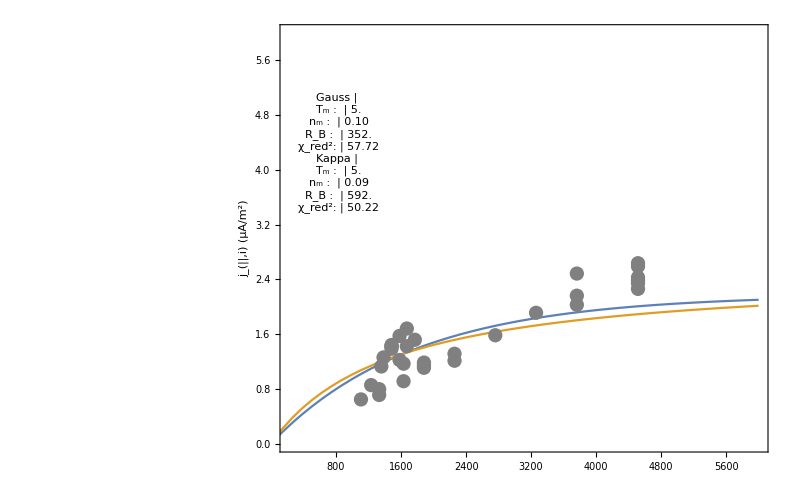
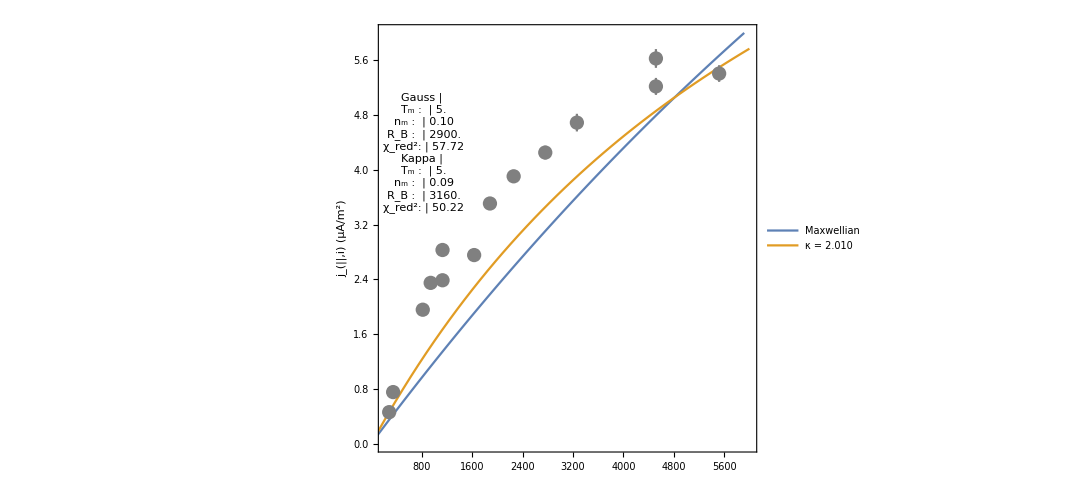
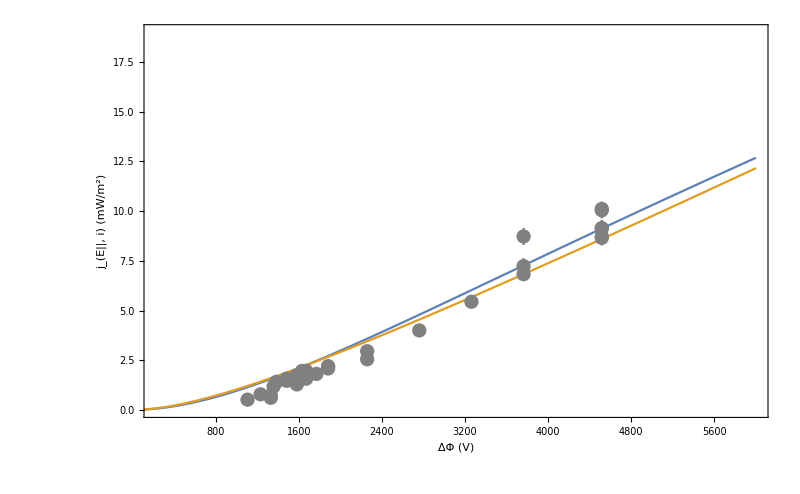
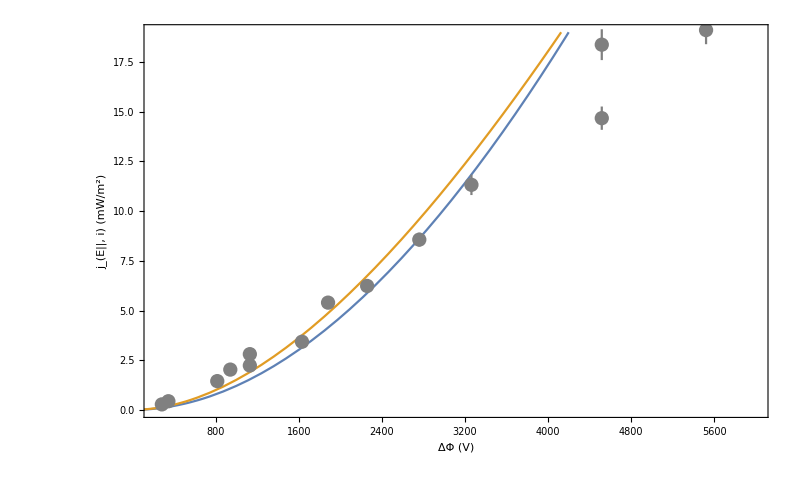
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
doubledPlot=Grid[{{doubledJVPlot1,doubledJVPlot2},{doubledJeVPlot1,doubledJeVPlot2}}]
```

Param tables

### J-V params

```mathematica
kFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
kFitN | 0.0788489 | 18.0635 | 0.0043651 | 0.996563
kFitT | 20.0084 | 211292. | 0.0000946954 | 0.999925
kFitRB | 999996. | 413.953 | 2415.72 | 1.33998×10^-53
kFitKappa | 1.5077 | 82.2571 | 0.0183292 | 0.985567

```mathematica
gFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
gFitN | 0.737783 | 2.50754 | 0.294226 | 0.771617
gFitT | 20. | 189.449 | 0.10557 | 0.916976
gFitRB | 336621. | 1.19817×10^10 | 0.0000280946 | 0.999978

### J_E-V params

```mathematica
kFitJeV["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
kFitN | 0.590468 | 12.8417 | 0.0459806 | 0.963806
kFitT | 20.0001 | 209.717 | 0.0953669 | 0.925022
kFitRB | 239189. | 4.5854×10^9 | 0.0000521631 | 0.999959
kFitKappa | 2.43713 | 84.7723 | 0.0287491 | 0.977365

```mathematica
gFitJeV["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
gFitN | 0.762078 | 0.387809 | 1.96508 | 0.063448
gFitT | 20. | 47.5033 | 0.421023 | 0.678228
gFitRB | 330538. | 6.09865×10^9 | 0.0000541986 | 0.999957

### Params from combined fit

```mathematica
kCombFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
kFitRB | 805633. | 8.95543×10^9 | 0.0000899603 | 0.999929
kFitT | 20. | 157.058 | 0.127342 | 0.899278
kFitN | 0.491447 | 1.8178 | 0.270352 | 0.788213
kFitKappa | 2.0396 | 0.791263 | 2.57765 | 0.0135471

```mathematica
gCombFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
gFitRB | 450860. | 4.64319×10^9 | 0.0000971014 | 0.999923
gFitT | 20. | 30.7434 | 0.650545 | 0.518801
gFitN | 0.738934 | 0.408339 | 1.80961 | 0.0773503